Here’s a notebook on Numerical Integration to support Rich Brower’s High Performance Computing class. Prepared by Evan S Weinberg. 2/1/2016 and Modified by Rich Brower 2/2/2019

This notebook will compute the 1D integral of a user-specified function on a user supplied interval, both exactly using Mathematica’s built in functions, and explicitly using different integration rules with a specified number of sub-intervals.

Specify the function:

```mathematica
func[x_]:=Sin[x]
```

What is the lower and upper limit of the integral?

```mathematica
xmin = 0;
xmax = 1;
```

How many sub-intervals should we use for numerical integration?

```mathematica
ninterval =10
```

10

The lower and upper limits combined with the number of intervals gives the step size.

```mathematica
h=(xmax-xmin)/ninterval;
```

First, let’s compute the exact integral with built-in Mathematica functions. The function “NumberForm” forces more output digits.

```mathematica
exactAnswer=Integrate[func[x], {x, xmin, xmax}];
```

```mathematica
N[exactAnswer]
```

0.459698

Next, we’ll use the trapezoidal rule.

```mathematica
trapAnswer=Sum[N[h/2*(func[xmin+i*h]+func[xmin+(i+1)*h])], {i, 0, ninterval-1}];
NumberForm[trapAnswer,15]
```

0.459314548857976

Now we’ll hop to Simpson’s rule. Simpson’s rule uses intervals of length “2h”, so you may get weird results if “ninterval” is odd!

```mathematica
simpAnswer=Sum[N[h/3*(func[xmin+2 i h]+4*func[xmin+(2 i+1)*h]+func[xmin+(2 i+2)*h])], {i, 0, ninterval/2-1}];
NumberForm[simpAnswer,15]
```

0.459697949823821

Last, we’ll use Gaussian quadrature with 3 points per interval. This uses the “change of interval” equation from the “Gaussian quadrature” Wikipedia article, where the “w_i” and “x_i” come from the Gauss-Legendre quadrature table.

```mathematica
gaussAnswer=Sum[N[h*(5/9*func[xmin+(2 i+1)*h-Sqrt[3/5]*h]+8/9*func[xmin+(2 i +1)*h]+5/9*func[xmin+(2 i +1)*h+Sqrt[3/5]*h])],{i,0,ninterval/2-1}];
NumberForm[gaussAnswer,15]
```

0.459697694146474

Let’s compare the relative errors.

Trapezoidal:

```mathematica
(trapAnswer-exactAnswer)/exactAnswer
```

-0.000833472

Simpsons:

```mathematica
(simpAnswer-exactAnswer)/exactAnswer
```

5.56218×10^-7

Gaussian quadrature:

```mathematica
(gaussAnswer-exactAnswer)/exactAnswer
```

3.17894×10^-11

You’ll see that Gaussian quadrature does really well, even with a small number of intervals! I started using just 10 on (0,1). Play around with some other functions. Some good exercises include:
 - x^n. Start from n = 1, and keep increasing n. At what values of “n” do the approximate integrals stop giving the exact answer?
 - 4/(1+x^2) on the interval (0,1). What are we approximating? (Hint: look at the exact answer!)
 - Set the lower limit to 10^(-1) (keep the upper as 1), and try integrating cos(1/x). How good are the approximations if you change the lower limit to 10^(-2)? 10^(-3)? Why is it so difficult to numerically integrate cos(1/x)?
 
 For fun can try overlapping the Gaussian intervals with h/2 to get an even better form.

```mathematica
ninterval  = ninterval/2
h=(xmax-xmin)/ninterval;
gaussAnswerOverlapping=Sum[N[h/2*(5/9*func[xmin+(i+0.5)*h-Sqrt[3/5]*h/2]+8/9*func[xmin+(i+0.5)*h]+5/9*func[xmin+(i+0.5)*h+Sqrt[3/5]*h/2])],{i,0,ninterval-1}];
NumberForm[gaussAnswerOverlapping,15]
```

5

0.459697694146474

```mathematica
(gaussAnswerOverlapping-exactAnswer)/exactAnswer
```

3.17897×10^-11

Here is an example of importing columns of data from the C program to use Mathematic for Plotting!  A good idea:
The following pulls a single column:
dataMatrix =Import[“/Users/richardbrower/Desktop/QuadPrecision/scaling.dat”,{”Data”,All, 4}]
Actually I preferred to import all the columns. Then Transposed to sect two.

```mathematica
dataMatrix =Transpose[ Import["/Users/richardbrower/Desktop/QuadPrecision/scaling.dat","Table"]]
```

{{4,16,64,256,1024,4096,16384,65536,262144,1048576,4194304,16777216,67108864,268435456,1073741824},{0.958944,0.956605,0.956459,0.95645,0.956449,0.956449,0.956449,0.956449,0.956449,0.956449,0.956449,0.956449,0.956449,0.956449,0.956449},{0.0024953,0.00015569,9.72957×10^-6,6.08094×10^-7,3.80059×10^-8,2.37537×10^-9,1.48457×10^-10,9.28646×10^-12,5.78759×10^-13,5.4956×10^-14,1.83187×10^-14,1.15463×10^-14,3.15303×10^-14,9.74554×10^-13,7.17071×10^-12},{0.0024953,0.00015569,9.72957×10^-6,6.08094×10^-7,3.80059×10^-8,2.37537×10^-9,1.4846×10^-10,9.27878×10^-12,5.79924×10^-13,3.62452×10^-14,2.26535×10^-15,1.41588×10^-16,8.85341×10^-18,5.55241×10^-19,3.28141×10^-20}}

```mathematica
MatrixForm[dataMatrix]
```

(4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824
0.958944 | 0.956605 | 0.956459 | 0.95645 | 0.956449 | 0.956449 | 0.956449 | 0.956449 | 0.956449 | 0.956449 | 0.956449 | 0.956449 | 0.956449 | 0.956449 | 0.956449
0.0024953 | 0.00015569 | 9.72957×10^-6 | 6.08094×10^-7 | 3.80059×10^-8 | 2.37537×10^-9 | 1.48457×10^-10 | 9.28646×10^-12 | 5.78759×10^-13 | 5.4956×10^-14 | 1.83187×10^-14 | 1.15463×10^-14 | 3.15303×10^-14 | 9.74554×10^-13 | 7.17071×10^-12
0.0024953 | 0.00015569 | 9.72957×10^-6 | 6.08094×10^-7 | 3.80059×10^-8 | 2.37537×10^-9 | 1.4846×10^-10 | 9.27878×10^-12 | 5.79924×10^-13 | 3.62452×10^-14 | 2.26535×10^-15 | 1.41588×10^-16 | 8.85341×10^-18 | 5.55241×10^-19 | 3.28141×10^-20)

This selects row 3 and row 5 from the above tablle and transposed them to do ListPlot -- I selected LogLog in thie case

```mathematica
doublelist= Transpose[{dataMatrix[[1]],dataMatrix[[3]]}]
```

{{4,0.0024953},{16,0.00015569},{64,9.72957×10^-6},{256,6.08094×10^-7},{1024,3.80059×10^-8},{4096,2.37537×10^-9},{16384,1.48457×10^-10},{65536,9.28646×10^-12},{262144,5.78759×10^-13},{1048576,5.4956×10^-14},{4194304,1.83187×10^-14},{16777216,1.15463×10^-14},{67108864,3.15303×10^-14},{268435456,9.74554×10^-13},{1073741824,7.17071×10^-12}}

```mathematica
quadlist= Transpose[{dataMatrix[[1]],dataMatrix[[4]]}]
```

{{4,0.0024953},{16,0.00015569},{64,9.72957×10^-6},{256,6.08094×10^-7},{1024,3.80059×10^-8},{4096,2.37537×10^-9},{16384,1.4846×10^-10},{65536,9.27878×10^-12},{262144,5.79924×10^-13},{1048576,3.62452×10^-14},{4194304,2.26535×10^-15},{16777216,1.41588×10^-16},{67108864,8.85341×10^-18},{268435456,5.55241×10^-19},{1073741824,3.28141×10^-20}}

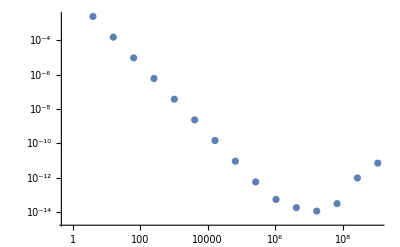

```mathematica
doublePlot = ListLogLogPlot[doublelist]
```

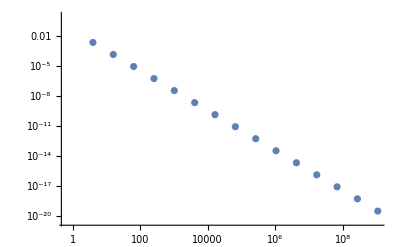

```mathematica
quadPlot = ListLogLogPlot[quadlist]
```

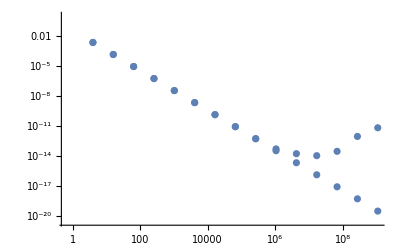

```mathematica
Show[ quadPlot,doublePlot]
```